```mathematica
Clear["Global`*"];
```

```mathematica
(*NND fitting formular*) 
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
(*pp[s_,ξb_]:=(ξb Gamma[3/2+ξb] HypergeometricU[1+ξb,1/2,(s^2 Gamma[ξb]^2)/(4 Gamma[1/2+ξb]^2)])/(√π ξsb[ξb]^2);*)
```

```mathematica
pp[s_,ξb_]:=(2^(-1-2 ξb) Gamma[ξb] Gamma[2+2 ξb] HypergeometricU[1+ξb,1/2,(s^2 Gamma[ξb]^2)/(4 Gamma[1/2+ξb]^2)])/Gamma[1/2+ξb]^2;
```

```mathematica
(* NV fitting formular*)
NV[L_?NumericQ,ξb_?NumericQ]:= L+((ξsb[ξb]/(√ξb))^-2-1) L^2
```

```mathematica
tablemod[{fileNND_String, fileNV_String, fileL_String}]:=Module[{nnd,filename,nlmNND,nv,nlmNV,l}, 
nnd=SetPrecision[Import[fileNND, "Table"],50];
filename=StringDelete[fileNND,"/home/xierr/Desktop/pato_all/pato_new_all/pato_new/DNA_NND_results/"|".txt"];
nlmNND=NonlinearModelFit[nnd/.{x_,y_}:>{x,Log[y]},Log[pp[s,Abs[ξb]]],ξb,s,PrecisionGoal->30,MaxIterations->10000];
nv=Import[fileNV, "Table"];
nlmNV=NonlinearModelFit[nv,NV[L,ξb],ξb,L];
l=Import[fileL];
{filename,ToExpression[l],N[nlmNV["BestFitParameters"][[1,2]]],N[nlmNND["RSquared"]],N[nlmNV["RSquared"]]}]
```

```mathematica
(*plotmod[file_String]:=Module[{nnd}, 
nnd=Import[file, "Table"];
ListPlot[nnd,PlotMarkers->Automatic]]*)
```

```mathematica
filesNND=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/DNA_NND_results"];
filesNV=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/DNA_NV_results"];
filesL=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/DNA_L_results"];
```

```mathematica
CloseKernels[];LaunchKernels[4];
DistributeDefinitions[tablemod,filesNND,filesNV,filesL];
```

```mathematica
TableForm[ParallelMap[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","λ","R_NND^2","R_NV^2"}}]
```

Sequence | ⟨L⟩ | λ | R_NND^2 | R_NV^2
A2ASS6 | 2.2358 | 1054.0861 | 0.9928 | 0.9890
A5ISW6 | 1.4478 | 1155.9176 | 0.9958 | 0.9707
A6QGY5 | 1.5129 | 1252.2650 | 0.9944 | 0.9736
A6U1Q5 | 1.4478 | 1155.9176 | 0.9958 | 0.9707
A8Z414 | 1.4550 | 1627.1431 | 0.9952 | 0.9663
C6KTB7 | 1.2754 | 4378.3480 | 0.9964 | 0.7713
C6KTD2 | 1.1490 | 3355.5201 | 0.9824 | 0.9070
G4SLH0 | 1.7536 | 42.5100 | 0.9960 | 0.9997
O01761 | 2.0781 | 116.7431 | 0.9974 | 0.9983
P0C6W0 | 1.9044 | 1834.5401 | 0.9936 | 0.9476
P0C6W1 | 1.8953 | 2047.0179 | 0.9890 | 0.9848
P0C6W2 | 2.2594 | 128.1605 | 0.9926 | 0.9920
P0C6W3 | 1.8839 | 1309.8835 | 0.9892 | 0.7958
P0C6W4 | 2.2927 | 1036.5411 | 0.9948 | 0.9883
P0C6W5 | 1.9727 | 933.8847 | 0.9921 | 0.9904
P0C6W6 | 2.2512 | 94.9777 | 0.9960 | 0.9913
P0C6W7 | 1.7658 | 2699.4189 | 0.9933 | 0.9935
P0C6X1 | 1.8564 | 1298.7541 | 0.9938 | 0.9763
P0C6X2 | 1.5165 | 1076.9503 | 0.9952 | 0.9944
P0C6X5 | 1.5294 | 1668.1823 | 0.9920 | 0.9795
P0C6X7 | 2.2457 | 115.8928 | 0.9956 | 0.9900
P0C6X9 | 2.0421 | 1574.2113 | 0.9928 | 0.9949
P0C6Y5 | 2.0015 | 1277.1938 | 0.9944 | 0.9875
P20929 | 2.2525 | 71.7038 | 0.9860 | 0.9954
Q008X6 | 1.9377 | 2076.5990 | 0.9928 | 0.9785
Q03001 | 2.0901 | 35.8902 | 0.9967 | 0.9972
Q09165 | 2.1539 | 1590.7264 | 0.9920 | 0.7808
Q09221 | 1.8955 | 2892.7133 | 0.9946 | 0.9006
Q09666 | 2.8447 | 31.2372 | 0.9927 | 0.9964
Q18DN4 | 2.2673 | 135.7529 | 0.9954 | 0.9958
Q23551 | 2.1455 | 1201.3115 | 0.9943 | 0.9921
Q2FYJ6 | 1.4538 | 774.0772 | 0.9951 | 0.9737
Q54CU4 | 1.7904 | 841.8959 | 0.9945 | 0.9762
Q54QG5 | 1.7123 | 7795.2445 | 0.9849 | 0.9774
Q555C6 | 1.4146 | 4119.4307 | 0.9905 | 0.9169
Q5CZC0 | 2.0244 | 24.2466 | 0.9886 | 0.9988
Q5HFY8 | 1.4522 | 1465.8010 | 0.9952 | 0.9686
Q5VST9 | 2.6241 | 10.6493 | 0.9935 | 0.9955
Q6GGX3 | 1.4528 | 1327.3349 | 0.9907 | 0.9699
Q6ZWQ0 | 2.4522 | 60.9646 | 0.9915 | 0.9898
Q7Z5P9 | 2.1569 | 24.3382 | 0.9936 | 0.9997
Q869L3 | 1.5019 | 245.0226 | 0.9909 | 0.9984
Q8CP76 | 1.3205 | 1574.9896 | 0.9964 | 0.8319
Q8I3Z1 | 1.0689 | 5192.0677 | 0.9917 | 0.9924
Q8NF91 | 2.1874 | 46.7486 | 0.9976 | 0.9923
Q8NWQ6 | 1.4571 | 1112.3306 | 0.9938 | 0.9704
Q8R0W0 | 2.5200 | 71.8729 | 0.9921 | 0.9924
Q8VHN7 | 2.1748 | 32.6434 | 0.9888 | 0.9965
Q8WXH0 | 2.2763 | 33.1601 | 0.9962 | 0.9951
Q8WXI7 | 2.6277 | 23.4348 | 0.9937 | 0.9942
Q8WZ42 | 2.0851 | 1705.0536 | 0.9915 | 0.9908
Q91ZU6 | 2.4429 | 51.1495 | 0.9930 | 0.9933
Q9I7U4 | 2.0291 | 16.5505 | 0.9956 | 0.9999
Q9QXZ0 | 2.3062 | 49.9320 | 0.9848 | 0.9911
Q9UPN3 | 2.2855 | 36.5614 | 0.9868 | 0.9934
W6RTA4 | 1.9497 | 287.7133 | 0.9946 | 0.9981

```mathematica
(*OutputForm[TableForm[Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","β","f_NV","ξ_NV","R_NND^2","R_NV^2"}}]]>>"test"*)
```

```mathematica
(*Export["/home/xierr/Desktop/tableIII.dat",Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]}];*)
```

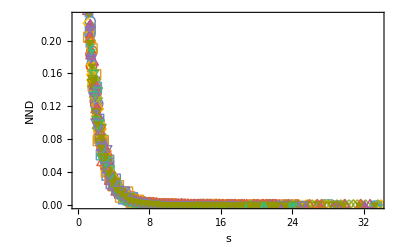

```mathematica
plotNND=ListPlot[Import[#,"Data"]&/@filesNND,PlotMarkers->Automatic, Frame->True,FrameLabel->{Style["s",FontFamily->"Times",Italic,15],Style["NND",FontFamily->"Times",Italic,15]}]
```

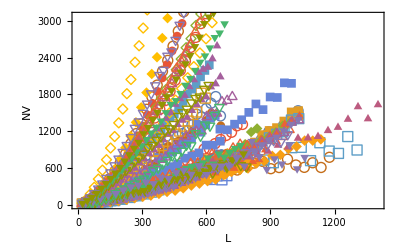

```mathematica
plotNV=ListPlot[Import[#,"Data"]&/@filesNV,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["L",FontFamily->"Times",Italic,15],Style["NV",FontFamily->"Times",Italic,15]}]
```